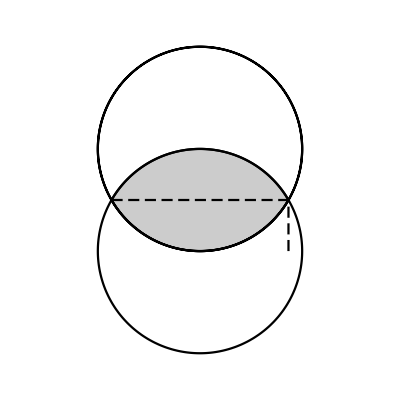

```mathematica
Quxian1=PolarPlot[1,{t,0,2Pi},PlotStyle->Black];
Quxian2=PolarPlot[2Sin[t],{t,0,2Pi},PlotStyle->Black];
Quxian3=Plot[1/2,{x,-Sqrt[3]/2,Sqrt[3]/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[3]/2,y},{y,0,1/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu=RegionPlot[x^2+y^2<=1&&x^2+(y-1)^2≤1,{x,-1,1},{y,0,1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-1.6,1.6},{-1.1,2.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,Ticks->None]
```

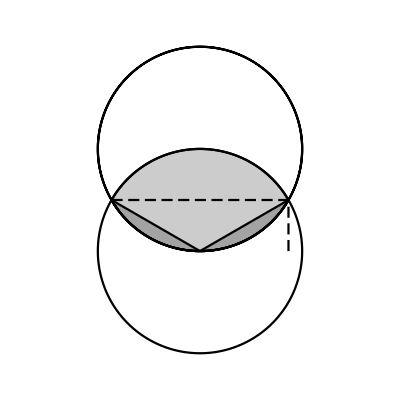

```mathematica
Quxian1=PolarPlot[1,{t,0,2Pi},PlotStyle->Black];
Quxian2=PolarPlot[2Sin[t],{t,0,2Pi},PlotStyle->Black];
Quxian3=Plot[1/2,{x,-Sqrt[3]/2,Sqrt[3]/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[3]/2,y},{y,0,1/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu3=Plot[{-Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,-Sqrt[3]/2,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,0,Sqrt[3]/2},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu=RegionPlot[x^2+y^2<=1&&x^2+(y-1)^2≤1,{x,-1,1},{y,0,1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quyu2,Quyu3,Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-1.6,1.6},{-1.1,2.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,Ticks->None]
```

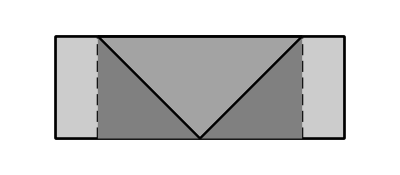

```mathematica
Quxian1=ParametricPlot[{Sqrt[2],y},{y,0,1},PlotStyle->Black];
Quxian2=ParametricPlot[{-Sqrt[2],y},{y,0,1},PlotStyle->Black];
Quxian3=Plot[{1,0},{x,-Sqrt[2],Sqrt[2]},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian4=ParametricPlot[{-1,y},{y,0,1},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian5=ParametricPlot[{1,y},{y,0,1},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu5=Plot[x,{x,0,1},Filling->Bottom,FillingStyle->GrayLevel[0.5],PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu4=Plot[-x,{x,-1,0},Filling->Bottom,FillingStyle->GrayLevel[0.5],PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu3=Plot[{1,x},{x,0,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{1,-x},{x,-1,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu=RegionPlot[-Sqrt[2]<=x≤Sqrt[2]&&0≤y≤1,{x,-Sqrt[2],Sqrt[2]},{y,0,1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quyu2,Quyu3,Quyu4,Quyu5,Quxian1,Quxian2,Quxian3,Quxian4,Quxian5,PlotRange->{{-1.6,1.6},{-0.2,1.2}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.4/3.2,Frame->False,Ticks->None]
```

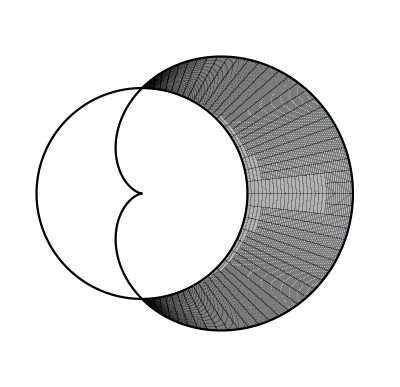

```mathematica
Quxian1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Black];
Quxian2=ParametricPlot[{(1+Cos[t])*Cos[t],(1+Cos[t])*Sin[t]},{t,0,2Pi},PlotStyle->Black];
Quyu=ParametricPlot[{r Cos[t],r Sin[t]},{t,-Pi/2,Pi/2},{r,1,1+Cos[t]},PlotStyle->Black];
Show[Quyu,Quxian1,Quxian2,PlotRange->{{-1.0,2.1},{-1.5,1.5}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->3.0/3.1,Frame->False,Ticks->None]
```

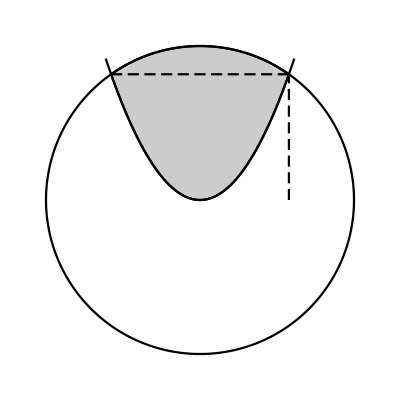

```mathematica
Quxian1=PolarPlot[Sqrt[6],{t,0,2Pi},PlotStyle->Black];
Quxian2=Plot[x^2,{x,-1.5,1.5},PlotStyle->Black];
Quxian3=Plot[2,{x,-Sqrt[2],Sqrt[2]},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[2],y},{y,0,2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu=RegionPlot[x^2≤y≤Sqrt[6-x^2],{x,-1.5,1.5},{y,0,Sqrt[6]+1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-2.6,2.6},{-2.6,2.6}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,Ticks->{{-2,-1,0,1,Sqrt[2],2},{-2,-1,0,1,2}}]
```

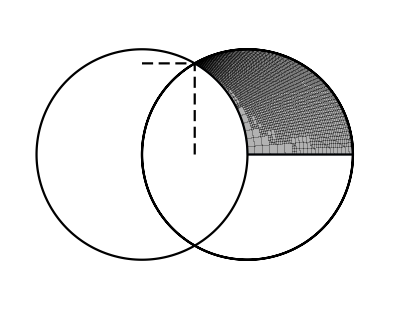

```mathematica
Quxian1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Black];
Quxian2=ParametricPlot[{(2Cos[t])*Cos[t],(2Cos[t])*Sin[t]},{t,0,2Pi},PlotStyle->Black];
Quxian3=Plot[0,{t,1,2},PlotStyle->Black];
Quxian4=ParametricPlot[{1/2,y},{y,0,Sqrt[3]/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian5=Plot[Sqrt[3]/2,{t,0,1/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu=ParametricPlot[{r Cos[t],r Sin[t]},{t,0,Pi/3},{r,1,2Cos[t]},PlotStyle->Black];
Show[Quyu,Quxian1,Quxian2,Quxian3,Quxian4,Quxian5,PlotRange->{{-1.0,2.1},{-1.2,1.2}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.4/3.1,Frame->False,Ticks->{{-1,0,1/2,1,2},{-1,0,Sqrt[3]/2,1}}]
```

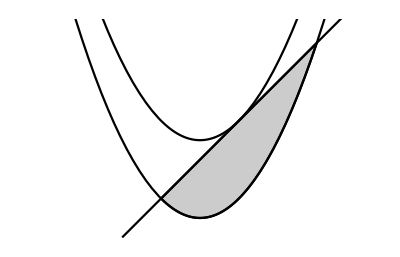

```mathematica
Quxian1=Plot[x^2+1,{x,-2,2},PlotStyle->Black];
Quxian2=Plot[x^2,{x,-2,2},PlotStyle->Black];
Quxian3=Plot[x-0.5+1.25,{x,-1,2},PlotStyle->Black];
Quyu=RegionPlot[x^2≤y≤x-0.5+1.25,{x,-1.5,1.5},{y,0,Sqrt[6]+1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,Quxian3,PlotRange->{{-2.1,2.1},{-0.2,2.5}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.7/4.2,Frame->False,Ticks->None]
```

```mathematica
P1=Plot3D[{z=x-y},{x,-1,3},{y,-1.2,1.2},BoxRatios->{4,2.4,6},PlotStyle->{Blue,Opacity[0.6]}];
P2=Plot3D[{z=0},{x,-1,3},{y,-1.2,1.2},BoxRatios->{4,2.4,1},PlotStyle->{Green,Opacity[0.6]}];
P3=ParametricPlot3D[{2Cos[theta]Cos[theta],2Cos[theta]Sin[theta],z},{theta,0,2Pi},{z,-1,3},AspectRatio->2,PlotStyle->{Opacity[0.6]}];
Show[P1,P2,P3]
```

```mathematica
Integrate[r^2*Sqrt[1+4r^2],{r,0,1}]
```

1/64 (18 √5-ArcSinh[2])

WolframAlphaQueryResults

ArcSinh[2]

```mathematica
Integrate[Abs[y*Sqrt[x^2+y^2]]Sqrt[1+4x^2+4y^2],{x,-1,1},{y,-1,1},WorkingPrecision->100]
```

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 3.78921829970228497826481023541406313655558339874839480575719057864679976319136514586822034934016107386225115106925386835722410147963860868145099305369 和 1.2494718779722413071427277685940374845906502043068648372964429854546602389962883926223657771348080684895111404131962236248541479777535757057100640443×10^-15.

3.789218299702284978264810235414063136555583398748394805757190578646799763191365145868220349340161074

```mathematica
NIntegrate[Abs[r*Sin[theta]*r]r Sqrt[1+4r^2],{theta,0,2Pi},{r,0,1}]
```

1.89672

```mathematica
N[(25Sqrt[5]+1)/30]
```

1.89672

```mathematica
PLTPS=100;
R1=RegionPlot3D[Sqrt[y^2+z^2]≤x≤2,{x,1,2},{y,-2,2},{z,-2,2},Axes->False, BoxRatios->{1,1,2},PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->PLTPS];
P2=ParametricPlot3D[{0,r Cos[theta],r Sin[theta]},{theta,0,2Pi},{r,1,2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.3]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{0,r Cos[theta],r Sin[theta]},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.7]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{x,Cos[theta],Sin[theta]},{theta,0,2Pi},{x,1,2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Red,Opacity[0.7]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{2.8,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-2.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-2.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[G1,R1,P2,P3,ViewPoint->{10,-40,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
R1=RegionPlot3D[x^2+y^2≤2z^2+1,{x,-3,3},{y,-3,3},{z,1,2},Axes->False,PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->PLTPS];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,Sqrt[3],3},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.3]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,Sqrt[3]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.7]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3.5,0,0},{3.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-3.5,0},{0,3.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{7,7,3}];
Show[G1,R1,ViewPoint->{10,-40,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{theta,0,2Pi},{r,0,3/2*Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.8]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],Sqrt[9-r^2]},{theta,0,2Pi},{r,0,3/2*Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.8]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,3/2*Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3.5,0,0},{3.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,3.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-3.5,0},{0,3.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{7,7,4}];
Show[G1,P2,P3,ViewPoint->{10,-40,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{0,y,z},{y,-3.5,3.5},{z,0,5},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{0,y,1/2y^2},{y,-2Sqrt[2],2Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[1]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2/2},{theta,0,2Pi},{r,0,2Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.8]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{r Cos[theta],r Sin[theta],4},{theta,0,2Pi},{r,0,2Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Purple,Opacity[0.8]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3.5,0,0},{3.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,5}}]},{Black,Arrowheads[.03],Arrow[{{0,-3.5,0},{0,3.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{7,7,4}];
Show[G1,P1,P2,P3,P4,ViewPoint->{20,20,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{3Sin[phi]Cos[theta],3 Sin[phi]Sin[theta],3 Cos[phi]},{phi,0,Pi/3},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{3Sin[phi]Cos[theta],3 Sin[phi]Sin[theta],3+3 Cos[phi]},{phi,2Pi/3,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-4,0,0},{4,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,3.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-4,0},{0,4,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{8,8,4}];
Show[G1,P1,P2,ViewPoint->{20,20,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

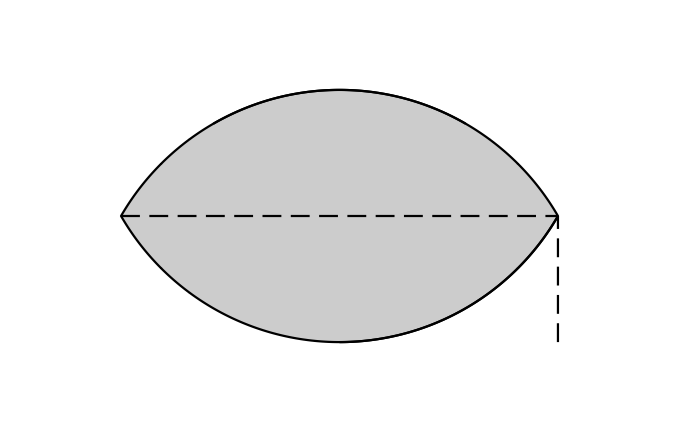

```mathematica
Quxian1=PolarPlot[1,{t,Pi/3,2Pi/3},PlotStyle->Black];
Quxian2=PolarPlot[2Sin[t],{t,0,Pi/6},PlotStyle->Black];
Quxian3=Plot[1/2,{x,-Sqrt[3]/2,Sqrt[3]/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[3]/2,y},{y,0,1/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu3=Plot[{-Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,-Sqrt[3]/2,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,0,Sqrt[3]/2},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu=RegionPlot[x^2+y^2<=1&&x^2+(y-1)^2≤1,{x,-1,1},{y,0,1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-0.9-0.2,0.9+0.2},{-0.2,1.2}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.4/2.2,Frame->False,Ticks->None]
```

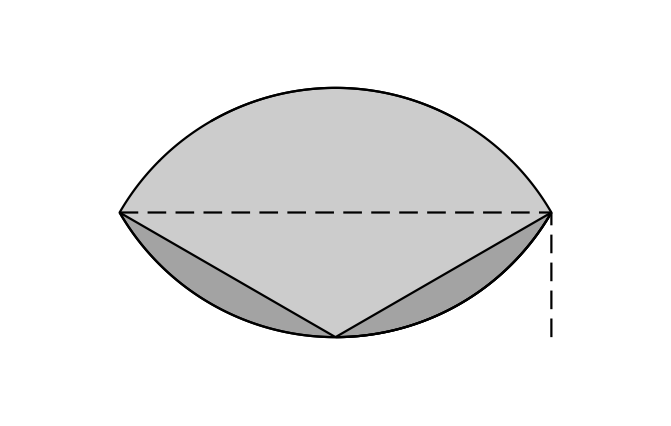

```mathematica
Quxian1=PolarPlot[1,{t,Pi/3,2Pi/3},PlotStyle->Black];
Quxian2=PolarPlot[2Sin[t],{t,0,Pi/6},PlotStyle->Black];
Quxian3=Plot[1/2,{x,-Sqrt[3]/2,Sqrt[3]/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[3]/2,y},{y,0,1/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu3=Plot[{-Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,-Sqrt[3]/2,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,0,Sqrt[3]/2},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu=RegionPlot[x^2+y^2<=1&&x^2+(y-1)^2≤1,{x,-1,1},{y,0,1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quyu2,Quyu3,Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-0.9-0.2,0.9+0.2},{-0.2,1.2}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.4/2.2,Frame->False,Ticks->None]
```

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{Sqrt[2]Cos[theta],Sqrt[2]Sin[theta],z},{theta,0,2Pi},{z,0,1},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],1},{theta,0,2Pi},{r,0,Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.75]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Purple,Opacity[0.5]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-Sqrt[2]-0.5,0,0},{Sqrt[2]+0.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-Sqrt[2]-0.5,0},{0,Sqrt[2]+0.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{2Sqrt[2]+1,2Sqrt[2]+1,2}];
Show[G1,P1,P2,P3,P4,ViewPoint->{20,20,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{3Sin[phi]Cos[theta],3Sin[phi]Sin[theta],3Cos[phi]},{phi,0,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3.5,0,0},{3.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-3.5},{0,0,3.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-3.5,0},{0,3.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{1,1,1}];
Show[G1,P1,ViewPoint->{20,20,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

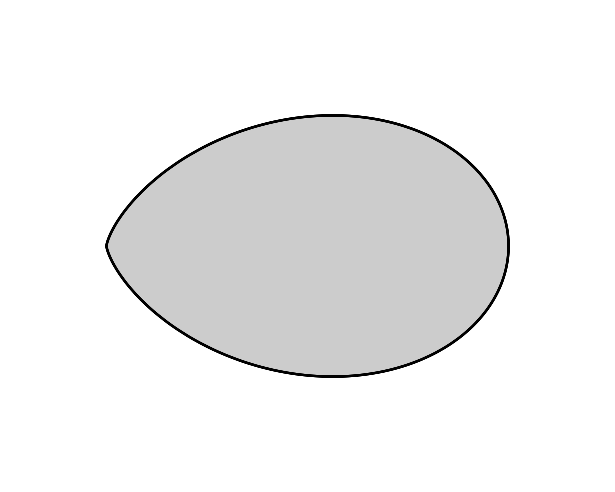

```mathematica
Quxian1=PolarPlot[8Cos[theta]^3,{theta,0,2Pi},PlotStyle->Black];
Quxian2=PolarPlot[2Sin[t],{t,0,Pi/6},PlotStyle->Black];
Quxian3=Plot[1/2,{x,-Sqrt[3]/2,Sqrt[3]/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[3]/2,y},{y,0,1/2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu3=Plot[{-Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,-Sqrt[3]/2,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{Sqrt[3]/3*x,1-Sqrt[1-x^2]},{x,0,Sqrt[3]/2},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu=RegionPlot[(x^2+y^2)^2≤8x^3,{x,-1,10},{y,-4,4},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,PlotRange->{{-1,9},{-4,4}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->8/10,Frame->False,Ticks->None]
```

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{Sqrt[6]Sin[phi]Cos[theta],Sqrt[6] Sin[phi]Sin[theta],Sqrt[6] Cos[phi]},{phi,0,Pi/2},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2},{r,0,Sqrt[Sqrt[6]]},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3,0,0},{3,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,3}}]},{Black,Arrowheads[.03],Arrow[{{0,-3,0},{0,3,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{6,6,3.5}];
Show[G1,P1,P2,ViewPoint->{20,20,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

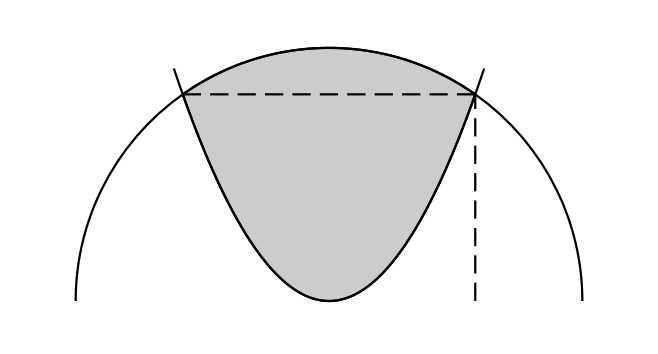

```mathematica
Quxian1=PolarPlot[Sqrt[6],{t,0,Pi},PlotStyle->Black];
Quxian2=Plot[x^2,{x,-1.5,1.5},PlotStyle->Black];
Quxian3=Plot[2,{x,-Sqrt[2],Sqrt[2]},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quxian4=ParametricPlot[{Sqrt[2],y},{y,0,2},PlotStyle->{Black,Dashing[{0.02,0.03-0.02}]}];
Quyu=RegionPlot[x^2≤y≤Sqrt[6-x^2],{x,-1.5,1.5},{y,0,Sqrt[6]+1},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,Quxian3,Quxian4,PlotRange->{{-2.6,2.6},{-0.2,2.6}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.8/5.2,Frame->False,Ticks->{{0,1,Sqrt[2],2},{-2,-1,0,1,2}}]
```

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2Cos[theta]Sin[theta]},{theta,0,Pi/3},{r,1,2Cos[theta]},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,Pi/3},{r,1,2Cos[theta]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Yellow,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{Cos[theta],Sin[theta],z},{theta,0,Pi/3},{z,0,Cos[theta]Sin[theta]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{2Cos[theta]Cos[theta],2Cos[theta]Sin[theta],z},{theta,0,Pi/3},{z,0,4Cos[theta]^2Cos[theta]Sin[theta]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Red,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-0.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-0.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{3,2,2}];
Show[G1,P1,P2,P3,P4,ViewPoint->{20,-40,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{Sin[phi]Cos[theta],Sin[phi]Sin[theta],Cos[phi]},{theta,0,2Pi},{phi,0,Pi/4},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{2Sin[phi]Cos[theta],2Sin[phi]Sin[theta],2Cos[phi]},{phi,0,Pi/4},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{theta,0,2Pi},{r,Sqrt[2]/2,Sqrt[2]},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Purple,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2,0,0},{2,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-2,0},{0,2,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{4,4,3}];
Show[G1,P1,P2,P3,ViewPoint->{20,20,5},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
F[x_,y_]=x^2+y^2+1;
DFx[x_,y_]=D[F[x,y],x];
DFy[x_,y_]=D[F[x,y],y];
PLTPS=100;
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2+1},{theta,0,2Pi},{r,0,1.5},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2},{theta,0,2Pi},{r,0,1.8},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{x,y,0.5^2+1+DFx[0,0.5]x+DFy[0,0.5](y-0.5)},{x,-2,2},{y,-1,2.5},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Red,Opacity[0.8]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{r Cos[theta],0.5+r Sin[theta],0},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Black,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.3,0,0},{2.3,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,1.8^2+0.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-2.3,0},{0,2.3,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{4.6,4.6,1.8^2+1}];
Show[G1,P1,P2,P3,P4,ViewPoint->{40,20,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

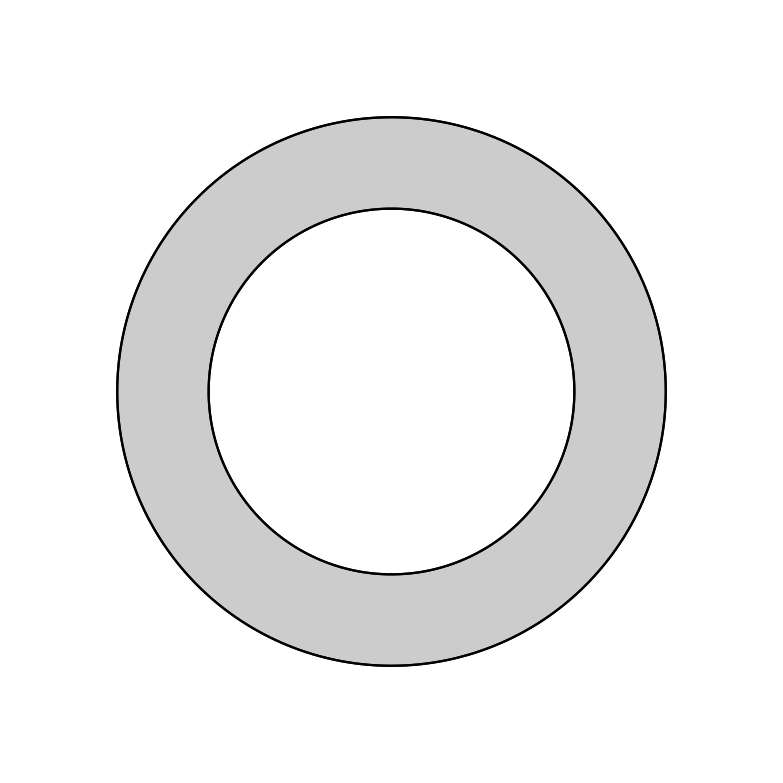

```mathematica
Quxian1=PolarPlot[2,{t,0,2Pi},PlotStyle->Black];
Quxian2=PolarPlot[3,{t,0,2Pi},PlotStyle->Black];
Quyu=RegionPlot[4≤x^2+y^2≤9,{x,-3,3},{y,-3,3},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,PlotRange->{{-3.5,3.5},{-3.5,3.5}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,Ticks->{{-3,-2,-2,1,2,3},{-3,-2,-1,0,1,2,3}}]
```

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{r Cos[theta],r Sin[theta],r^2},{theta,0,2Pi},{r,0,2.2},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{x,y,2x},{x,-0.5,2.2},{y,-2.2,2.2},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r  Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,2Cos[theta]},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Black,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,5.3}}]},{Black,Arrowheads[.03],Arrow[{{0,-2.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{5,5,5.8}];
Show[G1,P1,P2,P3,ViewPoint->{20,-30,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=RegionPlot3D[x^2+y^2+z^2≤2z,{x,-1,1},{y,-1,1},{z,0,2},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{3,3,3}];
Show[G1,P1,ViewPoint->{20,-20,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{3Sin[phi]Cos[theta],3 Sin[phi]Sin[theta],3 Cos[phi]+2},{phi,0,Pi/3},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{3Sin[phi]Cos[theta],3 Sin[phi]Sin[theta],3+3 Cos[phi]+2},{phi,2Pi/3,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{3r Cos[theta],3r Sin[theta],0},{r,0,Sqrt[3]/2},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[0.5]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{1,1,z},{z,3-Sqrt[9-1^2-1^2]+2,Sqrt[9-1^2-1^2]+2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P5=ParametricPlot3D[{1,1,z},{z,0,3-Sqrt[9-1^2-1^2]+2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Dashing[{0.005,0.0025}]},PlotPoints->PLTPS];
P6=ParametricPlot3D[{x,1,0},{x,-Sqrt[27/4-1^2],Sqrt[27/4-1^2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P7=ParametricPlot3D[{5,y,0},{y,-3Sqrt[3]/2,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P8=ParametricPlot3D[{x,-3Sqrt[3]/2,0},{x,0,5.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
P9=ParametricPlot3D[{x,3Sqrt[3]/2,0},{x,0,5.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
P10=ParametricPlot3D[{Sqrt[27/4-y^2],y,0},{y,-3Sqrt[3]/2,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Purple,Opacity[1]},PlotPoints->PLTPS];
P11=ParametricPlot3D[{-Sqrt[27/4-y^2],y,0},{y,-3Sqrt[3]/2,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Red,Opacity[1]},PlotPoints->PLTPS];
g1=Graphics3D[{Black,Arrowheads[.04],Arrow[{{1,1,1+2},{1,1,2+2}}]}];
g2=Graphics3D[{Black,Arrowheads[.04],Arrow[{{-Sqrt[27/4-1^2],1,0},{1.8,1,0}}]}];
g3=Graphics3D[{Black,Arrowheads[.04],Arrow[{{5,0,0},{5,1.7,0}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-4.0,0,0},{4.0,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,3.5+2}}]},{Black,Arrowheads[.03],Arrow[{{0,-4,0},{0,4,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{8,8,6}];
Show[G1,g1,g2,g3,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,ViewPoint->{20,-20,7},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PLTPS=100;
P1=ParametricPlot3D[{2Sin[phi]Cos[theta],2 Sin[phi]Sin[theta],3 Cos[phi]+1},{phi,0,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{2r Sin[3Pi/8]Cos[theta],2r Sin[3Pi/8]Sin[theta],3 Cos[3Pi/8]+1},{r,0,1},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[0.8]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{0,-4,z},{z,-2,4},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P5=ParametricPlot3D[{0,y,-2},{y,0,-4.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
P6=ParametricPlot3D[{0,y,4},{y,0,-4.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
P7=ParametricPlot3D[{5,y,0},{y,-3Sqrt[3]/2,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P8=ParametricPlot3D[{x,-3Sqrt[3]/2,0},{x,0,5.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
P9=ParametricPlot3D[{x,3Sqrt[3]/2,0},{x,0,5.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
P10=ParametricPlot3D[{Sqrt[27/4-y^2],y,0},{y,-3Sqrt[3]/2,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Purple,Opacity[1]},PlotPoints->PLTPS];
P11=ParametricPlot3D[{-Sqrt[27/4-y^2],y,0},{y,-3Sqrt[3]/2,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Red,Opacity[1]},PlotPoints->PLTPS];
g1=Graphics3D[{Black,Arrowheads[.04],Arrow[{{0,-4,0},{0,-4,3}}]}];
g2=Graphics3D[{Black,Arrowheads[.04],Arrow[{{-Sqrt[27/4-1^2],1,0},{1.8,1,0}}]}];
g3=Graphics3D[{Black,Arrowheads[.04],Arrow[{{5,0,0},{5,1.7,0}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-2.5,0,0},{2.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-2.5},{0,0,3.5+1}}]},{Black,Arrowheads[.03],Arrow[{{0,-2.5,0},{0,2.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{5,5,7.0}];
Show[G1,g1,P1,P3,P4,P5,P6,ViewPoint->{20,-20,7},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
Fx[theta_]=4Cos[theta];
Fy[theta_]=4Sin[theta];
Fz[theta_]=0;
DFx[theta_]=D[Fx[theta],theta];
DFy[theta_]=D[Fy[theta],theta];
DFz[theta_]=D[Fz[theta],theta];
PLTPS=100;
P1=ParametricPlot3D[{3Sin[phi]Cos[theta],3 Sin[phi]Sin[theta],3 Cos[phi]+2},{phi,0,Pi/3},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P2=ParametricPlot3D[{3Sin[phi]Cos[theta],3 Sin[phi]Sin[theta],3+3 Cos[phi]+2},{phi,2Pi/3,Pi},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{3r Cos[theta],3r Sin[theta],0},{r,0,Sqrt[3]/2},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[0.5]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{1,1,z},{z,3-Sqrt[9-1^2-1^2]+2,Sqrt[9-1^2-1^2]+2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P5=ParametricPlot3D[{1,1,z},{z,0,3-Sqrt[9-1^2-1^2]+2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Dashing[{0.005,0.0025}]},PlotPoints->PLTPS];
P6=ParametricPlot3D[{r Cos[Pi/4],r Sin[Pi/4],0},{r,0,3Sqrt[3]/2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P7=ParametricPlot3D[{4Cos[theta],4Sin[theta],0},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P8=ParametricPlot3D[{3Sqrt[3]/2Cos[theta],3Sqrt[3]/2Sin[theta],0},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Red,Opacity[1]},PlotPoints->PLTPS];
P9=ParametricPlot3D[{r Cos[Pi/4],r Sin[Pi/4],0},{r,3Sqrt[3]/2,4.2},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1],Thickness[0.0008]},PlotPoints->PLTPS];
g1=Graphics3D[{Black,Arrowheads[.02],Arrow[{{1,1,1+2},{1,1,2+2}}]}];
g2=Graphics3D[{Black,Arrowheads[.02],Arrow[{{0,0,0},{1.5,1.5,0}}]}];
g3=Graphics3D[{Black,Arrowheads[.02],Arrow[{{Fx[Pi/4-0.25],Fy[Pi/4-0.25],Fz[Pi/4-0.25]}-0.01{DFx[Pi/4-0.25],DFy[Pi/4-0.25],DFz[Pi/4-0.25]},{Fx[Pi/4],Fy[Pi/4],Fz[Pi/4]}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-5,0,0},{5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,3.5+2}}]},{Black,Arrowheads[.03],Arrow[{{0,-5,0},{0,5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{10,10,6}];
Show[G1,g1,g2,g3,P1,P2,P3,P4,P5,P6,P7,P8,P9,ViewPoint->{20,-20,7},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
Fx[phi_]=3.5 Sin[phi]Cos[Pi/4];
Fy[phi_]=3.5  Sin[phi]Sin[Pi/4];
Fz[phi_]=3.5Cos[phi];
DFx[phi_]=D[Fx[phi],phi];
DFy[phi_]=D[Fy[phi],phi];
DFz[phi_]=D[Fz[phi],phi];
Gx[theta_]=3.0 Cos[theta];
Gy[theta_]=3.0 Sin[theta];
Gz[theta_]=0;
DGx[theta_]=D[Gx[theta],theta];
DGy[theta_]=D[Gy[theta],theta];
DGz[theta_]=D[Gz[theta],theta];
PLTPS=10;
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{theta,0,2Pi},{r,0,3/2*Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Blue,Opacity[0.5]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],Sqrt[9-r^2]},{theta,0,2Pi},{r,0,3/2*Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Green,Opacity[0.5]},PlotPoints->PLTPS];
P4=ParametricPlot3D[{r Sin[Pi/6] Cos[Pi/4],r Sin[Pi/6] Sin[Pi/4],r Cos[Pi/6]},{r,0,3},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P5=ParametricPlot3D[{r Cos[Pi/4],r Sin[Pi/4],z},{r,0,3.5Sqrt[2]},{z,-0.5,4},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Yellow,Opacity[0.5]},PlotPoints->PLTPS];
P6=ParametricPlot3D[{r Cos[0],r Sin[0],z},{r,0,3.5},{z,-0.5,4},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Purple,Opacity[0.3]},PlotPoints->PLTPS];
P7=ParametricPlot3D[{r Cos[0],0,0},{r,0,3.5},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P8=ParametricPlot3D[{r Cos[Pi/4],r Sin[Pi/4],0},{r,0,3.5Sqrt[2]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P9=ParametricPlot3D[{3.5 Sin[phi]Cos[Pi/4],3.5  Sin[phi]Sin[Pi/4],3.5Cos[phi]},{phi,0,Pi/4},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Opacity[1]},PlotPoints->PLTPS];
P10=ParametricPlot3D[{r Sin[Pi/4]Cos[Pi/4],r Sin[Pi/4]Sin[Pi/4],r Cos[Pi/4]},{r,0,3.7},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black,Thickness[0.0008]},PlotPoints->PLTPS];
P11=ParametricPlot3D[{Gx[theta],Gy[theta],Gz[theta]},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Black},PlotPoints->PLTPS]
g1=Graphics3D[{Black,Arrowheads[.04],Arrow[{{0,0,0},{0.9,0.9,0.9Sqrt[6]}}]}];
g2=Graphics3D[{Black,Arrowheads[.04],Arrow[{{Fx[Pi/6],Fy[Pi/6],Fz[Pi/6]},{Fx[Pi/6],Fy[Pi/6],Fz[Pi/6]}+0.09{DFx[Pi/6],DFy[Pi/6],DFz[Pi/6]}}]}];
g3=Graphics3D[{Black,Arrowheads[.04],Arrow[{{Gx[Pi/4],Gy[Pi/4],Gz[Pi/4]}-0.09{DGx[Pi/4],DGy[Pi/4],DGz[Pi/4]},{Gx[Pi/4],Gy[Pi/4],Gz[Pi/4]}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3.5,0,0},{3.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,4}}]},{Black,Arrowheads[.03],Arrow[{{0,-3.5,0},{0,3.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{7,7,4}];
Show[G1,g1,g2,g3,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,ViewPoint->{10,40,10},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

-Graphics3D-

```mathematica
PLTPS=100;
R1=RegionPlot3D[x^2+y^2≤2z^2+1,{x,-3,3},{y,-3,3},{z,1,2},Axes->False,PlotStyle->{Green,Opacity[0.8]},Mesh->0,PlotPoints->PLTPS];
P2=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,Sqrt[3],3},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.3]},PlotPoints->PLTPS];
P3=ParametricPlot3D[{r Cos[theta],r Sin[theta],0},{theta,0,2Pi},{r,0,Sqrt[3]},Axes->False, BoxRatios->{1,1,0},Mesh->0,PlotStyle->{Gray,Opacity[0.7]},PlotPoints->PLTPS];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-3.5,0,0},{3.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-0.5},{0,0,2.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-3.5,0},{0,3.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}, BoxRatios->{7,7,3}];
Show[G1,R1,ViewPoint->{10,-40,5},Boxed->False,AxesOrigin->{0,0,0}]
```